# Discrete-time Quantum Walks (PoC)

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][dim/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][dim/2+1]]},
Inner[Chop[#1*#2.state.ConjugateTranspose[#2]]&,env["Probabilities"],#[dim/2+1]&/@env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*#2.state.ConjugateTranspose[#2]]&,env["Probabilities"],(#[Length[rho]/2+1]&/@env["Kraus"]),Plus]
]
```

## Examples

## Operadores

```mathematica
α=π/6.
```

0.523599

```mathematica
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
```

```mathematica
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
```

```mathematica
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
```

```mathematica
FuzzyOperator[n_]:=RotateLeft[IdentityMatrix[2*n,SparseArray],2]
```

## Examples

### Unitary DTQW

```mathematica
env=DTQWEnv[<|"Type"->"ForwardGrowing","Decoherent"->False,"Unitary"->UnitaryOperator|>]
```

DTQWEnv[…]

```mathematica
AbsoluteTiming[probs=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
Do[ρ=DTQWStep[ρ,env],150];
Total/@Partition[Diagonal@ρ,2]
];]
```

{3.27186,Null}

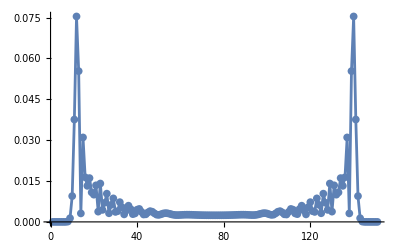

```mathematica
ListLinePlot[probs,
PlotRange->All,
Mesh->All
]
```

### DTQW w/fuzzy

```mathematica
env1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.1},
"Kraus"->{IdentityMatrix[2*#]&,FuzzyOperator}
|>]
```

```mathematica
AbsoluteTiming[probs1=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
Do[ρ=DTQWStep[ρ,env1],150];
Total/@Partition[Diagonal@ρ,2]
];]
```